# A Quantum-Like for the International Interaction Game

## The International Interaction Backward Induction Model

Explain here the Signorino  tree based model

## A Quantum-Like Approach

### Normal form approach

We propose we can understand IIG as the sequence of two normal-form game - demands and crisis games
In each of these two game, both actors have a strategic set of two strategies, from which they choose simultaneously

demands game | D2 | nD2
D1 | crisis game | U1Acq2, U2Acq2
nD1 | U1Acq1, U2Acq1 | U1SQ, U2SQ

 crisis game  | F2 | nF2
F1 | U1War, U2War | U1Cap2, U2Cap2
nF1 | U1Cap1, U2Cap1 | U1Nego, U2Nego
(we need to deal with the fact that we do not distinguish utilities of War1 and War2 in normal form game - we currently use an average of the two)

we take Signorino formula for the conditional probability of choosing between the strategies given their utilities and the expected strategy of the other player
p(F1|F2) = exp(lambda*U1War)/(exp(lambda*U1War)+exp(lambda*U1Cap1))

which results in following probability amplitudes

```mathematica
(* for debugging *)
U1SQ=-0.23801; U1Acq2=1.025024; U1Acq1=-1.36844;U1Nego=-1.10122; U1Cap1=-2.25679; U1Cap2=1.051597;U1War1=-1.51882; U1War2=-1.963;
U2SQ = -0.57593; U2Acq2 = -1.51157; U2Acq1=0.627684;U2Nego=0.591662; U2Cap1=0.861688; U2Cap2=-1.52841;U2War1 = 0.808828; U2War2=0.817247;
λ = 1;
```

```mathematica
U1War = Mean[{U1War1,U1War2}]; 
U2War = Mean[{U2War1,U2War2}];
```

```mathematica
aF1afterF2[U1War_,U1Cap1_, λ_, θ1a_] := Sqrt[ⅇ^(λ U1War)/(ⅇ^(λ U1War)+ⅇ^(λ U1Cap1))] ⅇ^(ⅈ Re[θ1a]) ;
aNF1afterF2[U1War_,U1Cap1_, λ_, θ1a_] := Sqrt[ⅇ^(λ U1Cap1)/(ⅇ^(λ U1War)+ⅇ^(λ U1Cap1))] ⅇ^(ⅈ Re[θ1a]) ;
aF1afterNF2[U1Cap2_,U1Nego_, λ_, θ1b_] := Sqrt[ⅇ^(λ U1Cap2)/(ⅇ^(λ U1Cap2)+ⅇ^(λ U1Nego))] ⅇ^(ⅈ Re[θ1b]) ;
aNF1afterNF2[U1Cap2_,U1Nego_, λ_, θ1b_] := Sqrt[ⅇ^(λ U1Nego)/(ⅇ^(λ U1Cap2)+ⅇ^(λ U1Nego))] ⅇ^(ⅈ Re[θ1b]) ;
aF2afterF1[U2War_,U2Cap2_, λ_, θ2a_] := Sqrt[ⅇ^(λ U2War)/(ⅇ^(λ U2War)+ⅇ^(λ U2Cap2))] ⅇ^(ⅈ Re[θ2a]) ;
aNF2afterF1[U2War_,U2Cap2_, λ_, θ2a_] := Sqrt[ⅇ^(λ U2Cap2)/(ⅇ^(λ U2War)+ⅇ^(λ U2Cap2))] ⅇ^(ⅈ Re[θ2a]) ;
aF2afterNF1[U2Cap1_,U2Nego_, λ_, θ2b_] := Sqrt[ⅇ^(λ U2Cap1)/(ⅇ^(λ U2Cap1)+ⅇ^(λ U2Nego))] ⅇ^(ⅈ Re[θ2b]) ;
aNF2afterNF1[U2Cap1_,U2Nego_, λ_, θ2b_] := Sqrt[ⅇ^(λ U2Nego)/(ⅇ^(λ U2Cap1)+ⅇ^(λ U2Nego))] ⅇ^(ⅈ Re[θ2b]) ;
```

#### Probability of individual strategies, player 1

```mathematica
aF1 [pF2norm_,aF1afterF2_,aF1afterNF2_]:= (Sqrt[pF2norm]*aF1afterF2) + (Sqrt[1-pF2norm]*aF1afterNF2);
pF1 [aF1_]:= aF1 * Conjugate[aF1];

aNF1[pF2norm_,aNF1afterF2_,aNF1afterNF2_] := (Sqrt[pF2norm]*aNF1afterF2) + (Sqrt[1-pF2norm]*aNF1afterNF2);
pNF1[aNF1_] := aNF1 * Conjugate[aNF1];

pF1norm [pF1_, pNF1_]:= pF1 / (pF1+pNF1);
pNF1norm [pF1_, pNF1_]:= pNF1 / (pF1+pNF1);
```

pF1 = pF2 * pF1afterF2 + pNF2 * pF1afterNF2 + 2*Sqrt[pF2*pNF2]*aF1afterF2*aF1afterNF2*Cos[θ1a-θ1b]
pF1 depends only phase difference Δθ1 = θ1a-θ1b, as expected

#### Probability of individual strategies, player 2

```mathematica
aF2 [pF1norm_, aF2afterF1_, aF2afterNF1_]:= (Sqrt[pF1norm]*aF2afterF1) + (Sqrt[1-pF1norm]*aF2afterNF1);
pF2 [aF2_]:= aF2 * Conjugate[aF2];

aNF2[pF1norm_, aNF2afterF1_, aNF2afterNF1_] := (Sqrt[pF1norm]*aNF2afterF1) + (Sqrt[1-pF1norm]*aNF2afterNF1);
pNF2[aNF2_] := aNF2 * Conjugate[aNF2];

pF2norm [pF2_, pNF2_]:= pF2 / (pF2+pNF2);
pNF2norm [pF2_, pNF2_]:= pNF2 / (pF2+pNF2);
```

that gives us two equations with two variables (pF1norm, pF2norm) => unique set of pF1norm, pF2norm satisfying the conditions
in our balanced dataset, we have 375 cases (War1, War2, Cap1, Cap2, Nego) of crisis game, we can look at this stage of IIG, without combining it with demands game
we can look for what combination of Δθ1 and Δθ2 does the model has the highest fit with the empirical observations

#### adding the demand game

to add the demand stage of the game (needed for the comparability to Signorino and de Mesquita), we proceed analogically to crisis game

demands game | D2 | nD2
D1 | U1Cris, U2Cris | U1Acq2, U2Acq2
nD1 | U1Acq1, U2Acq1 | U1SQ, U2SQ

```mathematica
U1Cris := (pF1norm*pF2norm*U1War)+(pF1norm*(1-pF2norm)*U1Cap2)+((1-pF1norm)*pF2norm*U1Cap1)+((1-pF1norm)*(1-pF2norm)*U1Nego);
U2Cris := (pF1norm*pF2norm*U2War)+(pF1norm*(1-pF2norm)*U2Cap2)+((1-pF1norm)*pF2norm*U2Cap1)+((1-pF1norm)*(1-pF2norm)*U2Nego);
```

```mathematica
aD1afterD2[U1Cris_,U1Acq1_, λ_, θ3a_] := Sqrt[ⅇ^(λ U1Cris)/(ⅇ^(λ U1Cris)+ⅇ^(λ U1Acq1))] ⅇ^(ⅈ Re[θ3a]) ;
aND1afterD2[U1Cris_,U1Acq1_, λ_, θ3a_] := Sqrt[ⅇ^(λ U1Acq1)/(ⅇ^(λ U1Cris)+ⅇ^(λ U1Acq1))] ⅇ^(ⅈ Re[θ3a]) ;
aD1afterND2[U1Acq2_,U1SQ_, λ_, θ3b_] := Sqrt[ⅇ^(λ U1Acq2)/(ⅇ^(λ U1Acq2)+ⅇ^(λ U1SQ))] ⅇ^(ⅈ Re[θ3b]) ;
aND1afterND2[U1Acq2_,U1SQ_, λ_, θ3b_] := Sqrt[ⅇ^(λ U1SQ)/(ⅇ^(λ U1Acq2)+ⅇ^(λ U1SQ))] ⅇ^(ⅈ Re[θ3b]) ;
aD2afterD1[U2Cris_,U2Acq2_ ,λ_, θ4a_] := Sqrt[ⅇ^(λ U2Cris)/(ⅇ^(λ U2Cris)+ⅇ^(λ U2Acq2))] ⅇ^(ⅈ Re[θ4a]) ;
aND2afterD1[U2Cris_,U2Acq2_, λ_, θ4a_] := Sqrt[ⅇ^(λ U2Acq2)/(ⅇ^(λ U2Cris)+ⅇ^(λ U2Acq2))] ⅇ^(ⅈ Re[θ4a]);
aD2afterND1[U2Acq1_,U2SQ_, λ_, θ4b_] := Sqrt[ⅇ^(λ U2Acq1)/(ⅇ^(λ U2Acq1)+ⅇ^(λ U2SQ))] ⅇ^(ⅈ Re[θ4b]) ;
aND2afterND1[U2Acq1_,U2SQ_,  λ_, θ4b_] := Sqrt[ⅇ^(λ U2SQ)/(ⅇ^(λ U2Acq1)+ⅇ^(λ U2SQ))] ⅇ^(ⅈ Re[θ4b]) ;
```

```mathematica
aD1 [pD2norm_,aD1afterD2_,aD1afterND2_]:= (Sqrt[pD2norm]*aD1afterD2) + (Sqrt[1-pD2norm]*aD1afterND2);
pD1 [aD1_]:= aD1 * Conjugate[aD1];

aND1[pD2norm_,aND1afterD2_,aND1afterND2_] := (Sqrt[pD2norm]*aND1afterD2) + (Sqrt[1-pD2norm]*aND1afterND2);
pND1[aND1_] := aND1 * Conjugate[aND1];

pD1norm [pD1_, pND1_]:= pD1 / (pD1+pND1);
pND1norm [pD1_, pND1_]:= pND1 / (pD1+pND1);

aD2 [pD1norm_,aD2afterD1_,aD2afterND1_]:= (Sqrt[pD1norm]*aD2afterD1) + (Sqrt[1-pD1norm]*aD2afterND1);
pD2 [aD2_]:= aD2 * Conjugate[aD2];

aND2[pD1norm_,aND2afterD1_,aND2afterND1_] := (Sqrt[pD1norm]*aND2afterD1) + (Sqrt[1-pD1norm]*aND2afterND1);
pND2[aND2_] := aND2 * Conjugate[aND2];

pD2norm [pD2_, pND2_]:= pD2 / (pD2+pND2);
pND2norm [pD2_, pND2_]:= pND2 / (pD2+pND2);
```

now there are 4 phases which we can to solve for to find the best fit with the empirical observations
Δθ1 ... phase connected to the decision to “fight/not fight” of the 1st player
Δθ2 ... phase connected to the decision to “fight/not fight” of the 2nd player
Δθ3 ... phase connected to the decision to “demand/not demand” of the 1st player
Δθ4 ... phase connected to the decision to “demand/not demand” of the 2nd player

we can set Δθ1=Δθ3 and Δθ2=Δθ4 if necessary

## Functions for Optimization

```mathematica
FindCrisisEquilibrium[u1War_,u1Cap1_,u1Cap2_,u1Nego_,u2War_,
					u2Cap2_,u2Cap1_,u2Nego_,
					lambda_,ΔΘ1_,ΔΘ2_,maxIter_:100,tolerance_:10^-6,verbose_:False]:=

	Module[{pF1normCurrent=0.5,pF2normCurrent=0.5,pF1normNext,pF2normNext,
			a1F2,a1NF2,a1F1,a1NF1,p1F1,p1NF1,a2F1,
			θ1a,θ1b,θ2a,θ2b,pWar,pCap2,pCap1,pNego,a2NF1,a2F2,a2NF2,p2F2,p2NF2,
			iter=0,converged=False,iterationHistory={}},

	(*Set phase differences*)
	θ1a=ΔΘ1/2;
	θ1b=-ΔΘ1/2;
	θ2a=ΔΘ2/2;
	θ2b=-ΔΘ2/2;

	pWar=Re[pF1normCurrent*pF2normCurrent];
	pCap2=Re[pF1normCurrent*(1-pF2normCurrent)];
	pCap1=Re[(1-pF1normCurrent)*pF2normCurrent];
	pNego=Re[(1-pF1normCurrent)*(1-pF2normCurrent)];

	(* keep a log for debugging purposes *)
	If[verbose,
	AppendTo[iterationHistory,
			<|"Iteration"->0,
			"pF1"->Re[pF1normCurrent],
			"pF2"->Re[pF2normCurrent],
			"θ1a"->θ1a,"θ1b"->θ1b,
			"ΔΘ1"->ΔΘ1,
			"θ2a"->θ2a,
			"θ2b"->θ2b,
			"ΔΘ2"->ΔΘ2,
			"pWar"->Re[pWar],
			"pCap2"->Re[pCap2],
			"pCap1"->Re[pCap1],
			"pNego"->Re[pNego]|>
	]
	];
	
	While[iter<maxIter&&!converged,
	
	(*Calculate amplitudes for player 1*)
	a1F2=aF1afterF2[u1War,u1Cap1,lambda,θ1a];
	a1NF2=aNF1afterF2[u1War,u1Cap1,lambda,θ1a];
	a1F1=aF1[pF2normCurrent,a1F2,aF1afterNF2[u1Cap2,u1Nego,lambda,θ1b]];
	a1NF1=aNF1[pF2normCurrent,a1NF2,aNF1afterNF2[u1Cap2,u1Nego,lambda,θ1b]];
	p1F1=pF1[a1F1];
	p1NF1=pNF1[a1NF1];
	pF1normNext=pF1norm[p1F1,p1NF1];

	(*Calculate amplitudes for player 2*)
	a2F1=aF2afterF1[u2War,u2Cap2,lambda,θ2a];
	a2NF1=aNF2afterF1[u2War,u2Cap2,lambda,θ2a];
	a2F2=aF2[pF1normCurrent,a2F1,aF2afterNF1[u2Cap1,u2Nego,lambda,θ2b]];
	a2NF2=aNF2[pF1normCurrent,a2NF1,aNF2afterNF1[u2Cap1,u2Nego,lambda,θ2b]];
	p2F2=pF2[a2F2];
	p2NF2=pNF2[a2NF2];
	pF2normNext=pF2norm[p2F2,p2NF2];
	pWar=Re[pF1normCurrent*pF2normCurrent];
         pCap2=Re[pF1normCurrent*(1-pF2normCurrent)];
         pCap1=Re[(1-pF1normCurrent)*pF2normCurrent]; 
         pNego=Re[(1-pF1normCurrent)*(1-pF2normCurrent)];

	(*Calculate convergence before updating values*)
	converged=Abs[pF1normNext-pF1normCurrent]<tolerance&&Abs[pF2normNext-pF2normCurrent]<tolerance;

	(*Track iteration if verbose*)
	If[verbose,
	AppendTo[iterationHistory,
	<|"Iteration"->iter,
	"pF1"->Re[pF1normCurrent],
	"pF2"->Re[pF2normCurrent],
	"θ1a"->θ1a,
	"θ1b"->θ1b,
	"ΔΘ1"->ΔΘ1,
	"θ2a"->θ2a,
	"θ2b"->θ2b,
	"ΔΘ2"->ΔΘ2,
	"ΔpF1"->Abs[pF1normNext-pF1normCurrent],
	"ΔpF2"->Abs[pF2normNext-pF2normCurrent],
	"pWar"->pWar,
	"pCap2"->pCap2,
	"pCap1"->pCap1,
	"pNego"->pNego|>
	]];

	(*Update for next iteration*)
	pF1normCurrent=Re[pF1normNext];
	pF2normCurrent=Re[pF2normNext];
	iter++;
];

	(*Return equilibrium probabilities and outcomes*)
	<|"Converged"->converged,
	"Iterations"->iter,
	"pF1"->Re[pF1normCurrent],
	"pF2"->Re[pF2normCurrent],
	"pWar"->pWar,
	"pCap2"->pCap2,
	"pCap1"->pCap1,
	"pNego"->pNego,
	"IterationHistory"->If[verbose,iterationHistory,Null]|>
]
```

```mathematica
(*Full model with both crisis and demands games*)
(*Full model with both crisis and demands games*)FindFullEquilibrium[u1War_,u1Cap1_,u1Cap2_,u1Nego_,u1SQ_,u1Acq1_,u1Acq2_,u2War_,u2Cap2_,u2Cap1_,u2Nego_,u2SQ_,u2Acq1_,u2Acq2_,lambda_,ΔΘ1_,ΔΘ2_,ΔΘ3_,ΔΘ4_,maxIter_:100,tolerance_:10^-6,verbose_:False]:=Module[{crisisEq,u1Cris,u2Cris,pD1normCurrent=0.5,pD2normCurrent=0.5,pD1normNext,pD2normNext,a1D2,a1ND2,a1D1,a1ND1,p1D1,p1ND1,a2D1,a2ND1,a2D2,a2ND2,p2D2,p2ND2,crisisPWar,crisisPCap1,crisisPCap2,crisisPNego,θ3a,θ3b,θ4a,θ4b,pCrisis,pAcq2,pAcq1,pSQ,iter=0,converged=False,iterationHistory={}},(*Set phase differences for demands game*)θ3a=ΔΘ3/2;
θ3b=-ΔΘ3/2;
θ4a=ΔΘ4/2;
θ4b=-ΔΘ4/2;
(*First find crisis game equilibrium*)crisisEq=FindCrisisEquilibrium[u1War,u1Cap1,u1Cap2,u1Nego,u2War,u2Cap2,u2Cap1,u2Nego,lambda,ΔΘ1,ΔΘ2,maxIter,tolerance,verbose];
(*Extract the individual probability values*)crisisPWar=crisisEq["pWar"];
crisisPCap1=crisisEq["pCap1"];
crisisPCap2=crisisEq["pCap2"];
crisisPNego=crisisEq["pNego"];
(*Calculate expected crisis utilities*)u1Cris=crisisPWar*u1War+crisisPCap2*u1Cap2+crisisPCap1*u1Cap1+crisisPNego*u1Nego;
u2Cris=crisisPWar*u2War+crisisPCap2*u2Cap2+crisisPCap1*u2Cap1+crisisPNego*u2Nego;
(*Initialize demand game probabilities*)pCrisis=Re[pD1normCurrent*pD2normCurrent];
pAcq2=Re[pD1normCurrent*(1-pD2normCurrent)];
pAcq1=Re[(1-pD1normCurrent)*pD2normCurrent];
pSQ=Re[(1-pD1normCurrent)*(1-pD2normCurrent)];
(*Record initial state if verbose*)If[verbose,AppendTo[iterationHistory,<|"Iteration"->0,"pD1"->Re[pD1normCurrent],"pD2"->Re[pD2normCurrent],"θ3a"->θ3a,"θ3b"->θ3b,"ΔΘ3"->ΔΘ3,"θ4a"->θ4a,"θ4b"->θ4b,"ΔΘ4"->ΔΘ4,"pCrisis"->pCrisis,"pAcq2"->pAcq2,"pAcq1"->pAcq1,"pSQ"->pSQ|>]];
(*Now find demands game equilibrium*)While[iter<maxIter&&!converged,(*Calculate amplitudes for player 1*)a1D2=aD1afterD2[u1Cris,u1Acq1,lambda,θ3a];
a1ND2=aND1afterD2[u1Cris,u1Acq1,lambda,θ3a];
a1D1=aD1[pD2normCurrent,a1D2,aD1afterND2[u1Acq2,u1SQ,lambda,θ3b]];
a1ND1=aND1[pD2normCurrent,a1ND2,aND1afterND2[u1Acq2,u1SQ,lambda,θ3b]];
p1D1=pD1[a1D1];
p1ND1=pND1[a1ND1];
pD1normNext=pD1norm[p1D1,p1ND1];
(*Calculate amplitudes for player 2*)a2D1=aD2afterD1[u2Cris,u2Acq2,lambda,θ4a];
a2ND1=aND2afterD1[u2Cris,u2Acq2,lambda,θ4a];
a2D2=aD2[pD1normCurrent,a2D1,aD2afterND1[u2Acq1,u2SQ,lambda,θ4b]];
a2ND2=aND2[pD1normCurrent,a2ND1,aND2afterND1[u2Acq1,u2SQ,lambda,θ4b]];
p2D2=pD2[a2D2];
p2ND2=pND2[a2ND2];
pD2normNext=pD2norm[p2D2,p2ND2];
(*Update outcome probabilities*)pCrisis=Re[pD1normCurrent*pD2normCurrent];
pAcq2=Re[pD1normCurrent*(1-pD2normCurrent)];
pAcq1=Re[(1-pD1normCurrent)*pD2normCurrent];
pSQ=Re[(1-pD1normCurrent)*(1-pD2normCurrent)];
(*Check convergence*)converged=Abs[pD1normNext-pD1normCurrent]<tolerance&&Abs[pD2normNext-pD2normCurrent]<tolerance;
(*Track iteration if verbose*)If[verbose,AppendTo[iterationHistory,<|"Iteration"->iter,"pD1"->Re[pD1normCurrent],"pD2"->Re[pD2normCurrent],"θ3a"->θ3a,"θ3b"->θ3b,"ΔΘ3"->ΔΘ3,"θ4a"->θ4a,"θ4b"->θ4b,"ΔΘ4"->ΔΘ4,"ΔpD1"->Abs[pD1normNext-pD1normCurrent],"ΔpD2"->Abs[pD2normNext-pD2normCurrent],"pCrisis"->pCrisis,"pAcq2"->pAcq2,"pAcq1"->pAcq1,"pSQ"->pSQ|>]];
(*Update for next iteration*)pD1normCurrent=Re[pD1normNext];
pD2normCurrent=Re[pD2normNext];
iter++;];
(*Return full equilibrium probabilities and outcomes*)<|"CrisisEquilibrium"-><|"pWar"->crisisPWar,"pCap1"->crisisPCap1,"pCap2"->crisisPCap2,"pNego"->crisisPNego,"pF1"->crisisEq["pF1"],"pF2"->crisisEq["pF2"],"Converged"->crisisEq["Converged"],"Iterations"->crisisEq["Iterations"]|>,"DemandsConverged"->converged,"DemandsIterations"->iter,"pD1"->Re[pD1normCurrent],"pD2"->Re[pD2normCurrent],"pCrisis"->pCrisis,"pAcq2"->pAcq2,"pAcq1"->pAcq1,"pSQ"->pSQ,"ExpectedUtility1"->pCrisis*u1Cris+pAcq2*u1Acq2+pAcq1*u1Acq1+pSQ*u1SQ,"ExpectedUtility2"->pCrisis*u2Cris+pAcq2*u2Acq2+pAcq1*u2Acq1+pSQ*u2SQ,"DemandsIterationHistory"->If[verbose,iterationHistory,Null]|>]
```

```mathematica
(*Grid search to find optimal phase differences*)
(* make the optimization for 4 parmsinstead of 8 *)
FindOptimalPhases[dataSet_,lambda_,phaseGridSize_:10]:=Module[{phaseValues,bestFit=-Infinity,bestPhases,currentFit,results},

(*Create grid of phase values*)
phaseValues=Table[N[2π*i/phaseGridSize],{i,0,phaseGridSize-1}];

(*Grid search*)
bestPhases={};

(*For each combination of phases*)
Do[

(*Get equilibrium for this case*)
results=Table[
With[{row=dataSet[[i]]},
FindFullEquilibrium[row["U1War"],row["U1Cap1"],row["U1Cap2"],
				      row["U1Nego"],row["U1SQ"],row["U1Acq1"],row["U1Acq2"],
				       row["U2War"],row["U2Cap2"],row["U2Cap1"],row["U2Nego"],
				       row["U2SQ"],row["U2Acq1"],row["U2Acq2"],lambda,θ1a,θ1b,θ2a,θ2b,θ3a,θ3b,θ4a,θ4b]],{i,Length[dataSet]}];

(*Calculate fit using log-likelihood*)
currentFit=
Sum[
With[{row=dataSet[[i]],result=results[[i]]},
Which[row["groundtruth"]=="War",
		Log[result["CrisisEquilibrium"]["pWar"]],
	row["groundtruth"]=="Cap1",
		Log[result["CrisisEquilibrium"]["pCap1"]],
	row["groundtruth"]=="Cap2",
		Log[result["CrisisEquilibrium"]["pCap2"]],
	row["groundtruth"]=="Nego",
		Log[result["CrisisEquilibrium"]["pNego"]],
	row["groundtruth"]=="SQ",
		Log[result["pSQ"]],
	row["groundtruth"]=="Acq1",
	Log[result["pAcq1"]],
	row["groundtruth"]=="Acq2",
		Log[result["pAcq2"]],True,0]],{i,Length[dataSet]}];

(*Update best fit*)
If[currentFit>bestFit,bestFit=currentFit;
	bestPhases={θ1a,θ1b,θ2a,θ2b,θ3a,θ3b,θ4a,θ4b};],

(* iteration updates *)
{θ1a,phaseValues},
{θ1b,phaseValues},
{θ2a,phaseValues},
{θ2b,phaseValues},
{θ3a,phaseValues},
{θ3b,phaseValues},
{θ4a,phaseValues},
{θ4b,phaseValues}
];

(*Return best phases and fit*)
{"BestPhases"->bestPhases,
"LogLikelihood"->bestFit,
"Lambda"->lambda}
];
```

## Testing

```mathematica
(* Prepare the dataset in the format needed *)
```

```mathematica
data=Import["C:\\Users\\cmore\\Documents\\Github\\quantum_international_interaction_game\\Norm_Form\\first_dataset_with_SQ.csv","CSV","HeaderLines"->1];
```

```mathematica
dataset=Dataset[Association@@@(Rule@@@Transpose[{{"Agent1","Agent2","wrTu1sq","wrTu1ac1","wrTu1ac2","wrTu1neg","wrTu1cp1","wrTu1cp2","wrTu1wr1","wrTu1wr2","wrTu2sq","wrTu2ac2","wrTu2ac1","wrTu2neg","wrTu2cp2","wrTu2cp1","wrTu2wr2","wrTu2wr1","groundtruth"},#}]&/@data)];
```

```mathematica
dataset
```

Dataset[<>]

```mathematica
preparedData=
Table[<|"Agent1"->dataset[i,"Agent1"],"Agent2"->dataset[i,"Agent2"],"U1War"->(dataset[i,"wrTu1wr1"]+dataset[i,"wrTu1wr2"])/2,"U1Cap1"->dataset[i,"wrTu1cp1"],"U1Cap2"->dataset[i,"wrTu1cp2"],"U1Nego"->dataset[i,"wrTu1neg"],"U1SQ"->dataset[i,"wrTu1sq"],"U1Acq1"->dataset[i,"wrTu1ac1"],"U1Acq2"->dataset[i,"wrTu1ac2"],"U2War"->(dataset[i,"wrTu2wr1"]+dataset[i,"wrTu2wr2"])/2,"U2Cap1"->dataset[i,"wrTu2cp1"],"U2Cap2"->dataset[i,"wrTu2cp2"],"U2Nego"->dataset[i,"wrTu2neg"],"U2SQ"->dataset[i,"wrTu2sq"],"U2Acq1"->dataset[i,"wrTu2ac1"],"U2Acq2"->dataset[i,"wrTu2ac2"],"groundtruth"->dataset[i,"groundtruth"]|>,{i,Length[dataset]}];
```

```mathematica
preparedData
```

## Single Case Test

```mathematica
(* test a single case *)
```

```mathematica
sampleCase=preparedData[[1]]
```

<|Agent1→USA,Agent2→ESP,U1War→-1.74091,U1Cap1→-2.25679,U1Cap2→1.0516,U1Nego→-1.10122,U1SQ→-0.238012,U1Acq1→-1.36844,U1Acq2→1.02502,U2War→0.813038,U2Cap1→0.861688,U2Cap2→-1.52841,U2Nego→0.591662,U2SQ→-0.575933,U2Acq1→0.627684,U2Acq2→-1.51157,groundtruth→Cap2|>

```mathematica
(*Test the crisis equilibrium function with a single case*)
```

### Compute SubCrisis Game

```mathematica
result=
FindCrisisEquilibrium[sampleCase["U1War"],
					sampleCase["U1Cap1"],
					sampleCase["U1Cap2"],
					sampleCase["U1Nego"],
					sampleCase["U2War"],
					sampleCase["U2Cap2"],
					sampleCase["U2Cap1"],
					sampleCase["U2Nego"],
					1.0,π,3π/2,100,0.000001, True];
```

```mathematica
Print["Converged: ", result["Converged"]    ];
Print["Total Iterations: ", result["Iterations"]   ]; 
Print["Likelihood Player 1 Fighting: ", Re[result["pF1"]   ]]; 
Print["Likelihood Player 2 Fighting: ", Re[result["pF2"]   ]];  
Print["pWar: ", result["pWar"]   ];  
Print["pCap1: ", result["pCap1"]   ];  
Print["pCap2: ", result["pCap2"]   ];  
Print["pNego: ", result["pNego"]   ];
```

Converged: True

Total Iterations: 24

Likelihood Player 1 Fighting: 0.00853183

Likelihood Player 2 Fighting: 0.570044

pWar: 0.00486351

pCap1: 0.56518

pCap2: 0.00366831

pNego: 0.426288

### Get SubCrisis Game Results

```mathematica
history=result["IterationHistory"];
```

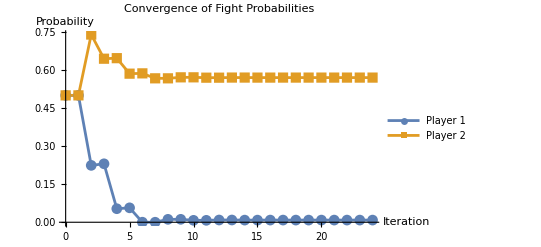

```mathematica
ListPlot[{
Table[{i,history[[i+1,"pF1"]]},
	  {i,0,Length[history]-1}],
Table[{i,history[[i+1,"pF2"]]},{i,0,Length[history]-1}]},
PlotLegends->{"Player 1","Player 2"},AxesLabel->{"Iteration","Probability"},PlotLabel->"Convergence of Fight Probabilities",Joined->True,Mesh->All,PlotMarkers->Automatic]
```

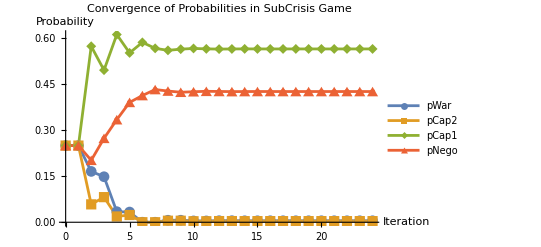

```mathematica
ListPlot[{
	 Table[{i,history[[i+1,"pWar"]]},{i,0,Length[history]-1}],
	 Table[{i,history[[i+1,"pCap2"]]},{i,0,Length[history]-1}],
	 Table[{i,history[[i+1,"pCap1"]]},{i,0,Length[history]-1}],
	 Table[{i,history[[i+1,"pNego"]]},{i,0,Length[history]-1}]
	},
PlotLegends->{"pWar","pCap2","pCap1","pNego"},AxesLabel->{"Iteration","Probability"},PlotLabel->"Convergence of Probabilities in SubCrisis Game",Joined->True,Mesh->All,PlotMarkers->Automatic]
```

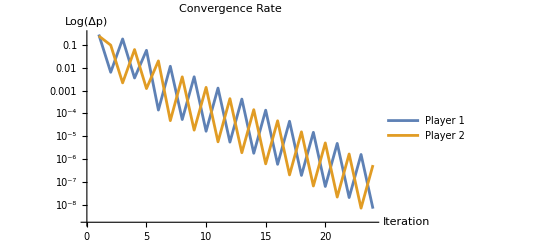

```mathematica
If[Length[history]>1,
ListLogPlot[{
Table[{i,history[[i+1,"ΔpF1"]]},
{i,1,Length[history]-1}],
Table[{i,history[[i+1,"ΔpF2"]]},
	{i,1,Length[history]-1}]},
PlotLegends->{"Player 1","Player 2"},AxesLabel->{"Iteration","Log(Δp)"},PlotLabel->"Convergence Rate",Joined->True]]
```

```mathematica
If[Length[history]>1,Grid[{{"Iteration","pF1","pF2","ΔpF1","ΔpF2", "θ1a", "θ1b", "θ2a", "θ2b", "ΔΘ1", "ΔΘ2"}}~Join~Table[{history[[i,"Iteration"]],
NumberForm[history[[i,"pF1"]],{4,4}],
NumberForm[history[[i,"pF2"]],{4,4}],
NumberForm[history[[i,"ΔpF1"]],{4,4}],
NumberForm[history[[i,"ΔpF2"]],{4,4}],
NumberForm[history[[i,"θ1a"]],{4,4}],
NumberForm[history[[i,"θ1b"]],{4,4}],
NumberForm[history[[i,"θ2a"]],{4,4}],
NumberForm[history[[i,"θ2b"]],{4,4}],
NumberForm[history[[i,"ΔΘ1"]],{4,4}],
NumberForm[history[[i,"ΔΘ2"]],{4,4}]
},
{i,2,Length[history]}],
Frame->All,Alignment->Center,Background->{None,{LightGray,None}}]]
```

Iteration | pF1 | pF2 | ΔpF1 | ΔpF2 | θ1a | θ1b | θ2a | θ2b | ΔΘ1 | ΔΘ2
0 | 0.5000 | 0.5000 | 0.2759 | 0.2397 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
1 | 0.2241 | 0.7397 | 0.0062 | 0.0952 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
2 | 0.2304 | 0.6445 | 0.1770 | 0.0022 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
3 | 0.0533 | 0.6466 | 0.0035 | 0.0611 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
4 | 0.0569 | 0.5855 | 0.0566 | 0.0012 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
5 | 0.0002 | 0.5867 | 0.0001 | 0.0195 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
6 | 0.0001 | 0.5672 | 0.0114 | 0.0000 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
7 | 0.0115 | 0.5671 | 0.0001 | 0.0039 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
8 | 0.0116 | 0.5711 | 0.0040 | 0.0000 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
9 | 0.0076 | 0.5711 | 0.0000 | 0.0014 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
10 | 0.0076 | 0.5697 | 0.0013 | 5.7680×10^-6 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
11 | 0.0088 | 0.5697 | 5.6020×10^-6 | 0.0004 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
12 | 0.0089 | 0.5702 | 0.0004 | 1.9330×10^-6 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
13 | 0.0084 | 0.5702 | 1.8300×10^-6 | 0.0001 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
14 | 0.0084 | 0.5700 | 0.0001 | 6.3150×10^-7 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
15 | 0.0086 | 0.5700 | 6.0280×10^-7 | 0.0000 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
16 | 0.0086 | 0.5701 | 0.0000 | 2.0810×10^-7 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
17 | 0.0085 | 0.5701 | 1.9800×10^-7 | 0.0000 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
18 | 0.0085 | 0.5700 | 0.0000 | 6.8360×10^-8 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
19 | 0.0085 | 0.5700 | 6.5130×10^-8 | 5.1710×10^-6 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
20 | 0.0085 | 0.5700 | 4.9260×10^-6 | 2.2480×10^-8 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
21 | 0.0085 | 0.5700 | 2.1410×10^-8 | 1.7000×10^-6 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
22 | 0.0085 | 0.5700 | 1.6190×10^-6 | 7.3890×10^-9 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2
23 | 0.0085 | 0.5700 | 7.0390×10^-9 | 5.5890×10^-7 | π/2 | -π/2 | (3 π)/4 | -(3 π)/4 | π | (3 π)/2

### Get Full Game Results

```mathematica
fullResult=FindFullEquilibrium[sampleCase["U1War"],sampleCase["U1Cap1"],sampleCase["U1Cap2"],sampleCase["U1Nego"],sampleCase["U1SQ"],sampleCase["U1Acq1"],sampleCase["U1Acq2"],sampleCase["U2War"],sampleCase["U2Cap2"],sampleCase["U2Cap1"],sampleCase["U2Nego"],sampleCase["U2SQ"],sampleCase["U2Acq1"],sampleCase["U2Acq2"],1.0,0,0,0,0,100,0.000001,True];
```

```mathematica
(*Print Crisis Game Results*)
crisisEq=fullResult["CrisisEquilibrium"];
Print["Crisis Game Results:"];
Print["  Converged: ",crisisEq["Converged"]];
Print["  Total Iterations: ",crisisEq["Iterations"]];
Print["  Likelihood Player 1 Fighting: ",crisisEq["pF1"]];
Print["  Likelihood Player 2 Fighting:} ",crisisEq["pF2"]];
Print["  pWar: ",crisisEq["pWar"]];
Print["  pCap1: ",crisisEq["pCap1"]];
Print["  pCap2: ",crisisEq["pCap2"]];
Print["  pNego: ",crisisEq["pNego"]];
```

Crisis Game Results:

Converged: True

Total Iterations: 9

Likelihood Player 1 Fighting: 0.727303

Likelihood Player 2 Fighting:} 0.804068

pWar: 0.5848

pCap1: 0.219267

pCap2: 0.142502

pNego: 0.0534303

```mathematica
(*Print Demands Game Results*)
Print["\nDemands Game Results:"];
Print["  Converged: ",fullResult["DemandsConverged"]];
Print["  Total Iterations: ",fullResult["DemandsIterations"]];
Print["  Likelihood Player 1 Demanding: ",fullResult["pD1"]];
Print["  Likelihood Player 2 Demanding: ",fullResult["pD2"]];
Print["  pCrisis: ",fullResult["pCrisis"]];
Print["  pAcq1: ",fullResult["pAcq1"]];
Print["  pAcq2: ",fullResult["pAcq2"]];
Print["  pSQ: ",fullResult["pSQ"]];
Print["\nExpected Utilities:"];
Print["  Player 1: ",fullResult["ExpectedUtility1"]];
Print["  Player 2: ",fullResult["ExpectedUtility2"]];
```

Demands Game Results:

Converged: True

Total Iterations: 7

Likelihood Player 1 Demanding: 0.581846

Likelihood Player 2 Demanding: 0.832536

pCrisis: 0.484408

pAcq1: 0.348129

pAcq2: 0.0974377

pSQ: 0.0700253

Expected Utilities:

Player 1: -1.08197

Player 2: 0.262553

```mathematica
demandsHistory=fullResult["DemandsIterationHistory"];
```

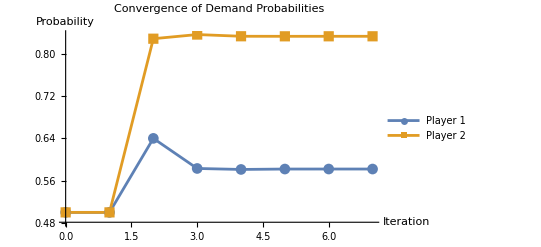

```mathematica
(*Plot convergence of demand probabilities*)ListPlot[{Table[{i,demandsHistory[[i+1,"pD1"]]},{i,0,Length[demandsHistory]-1}],Table[{i,demandsHistory[[i+1,"pD2"]]},{i,0,Length[demandsHistory]-1}]},PlotLegends->{"Player 1","Player 2"},AxesLabel->{"Iteration","Probability"},PlotLabel->"Convergence of Demand Probabilities",Joined->True,Mesh->All,PlotMarkers->Automatic]
```

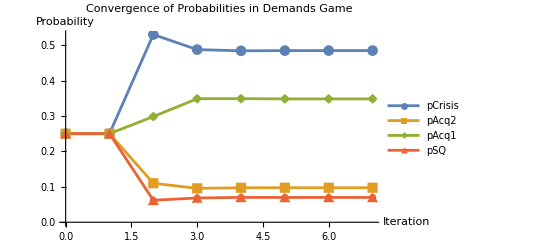

```mathematica
(*Plot convergence of outcome probabilities in demands game*)ListPlot[{Table[{i,demandsHistory[[i+1,"pCrisis"]]},{i,0,Length[demandsHistory]-1}],Table[{i,demandsHistory[[i+1,"pAcq2"]]},{i,0,Length[demandsHistory]-1}],Table[{i,demandsHistory[[i+1,"pAcq1"]]},{i,0,Length[demandsHistory]-1}],Table[{i,demandsHistory[[i+1,"pSQ"]]},{i,0,Length[demandsHistory]-1}]},PlotLegends->{"pCrisis","pAcq2","pAcq1","pSQ"},AxesLabel->{"Iteration","Probability"},PlotLabel->"Convergence of Probabilities in Demands Game",Joined->True,Mesh->All,PlotMarkers->Automatic]
```

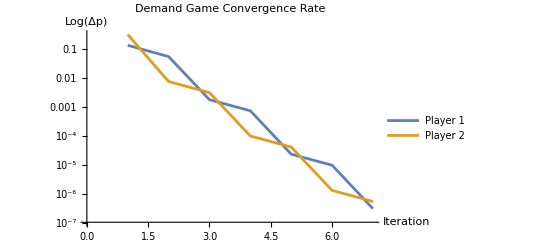

```mathematica
(*Plot convergence rate for demands game*)If[Length[demandsHistory]>1,ListLogPlot[{Table[{i,demandsHistory[[i+1,"ΔpD1"]]},{i,1,Length[demandsHistory]-1}],Table[{i,demandsHistory[[i+1,"ΔpD2"]]},{i,1,Length[demandsHistory]-1}]},PlotLegends->{"Player 1","Player 2"},AxesLabel->{"Iteration","Log(Δp)"},PlotLabel->"Demand Game Convergence Rate",Joined->True]]
```

```mathematica
(*Create detailed table of demand game iterations*)If[Length[demandsHistory]>1,Grid[{{"Iteration","pD1","pD2","ΔpD1","ΔpD2","θ3a","θ3b","θ4a","θ4b","ΔΘ3","ΔΘ4"}}~Join~Table[{demandsHistory[[i,"Iteration"]],NumberForm[demandsHistory[[i,"pD1"]],{4,4}],NumberForm[demandsHistory[[i,"pD2"]],{4,4}],If[i>1,NumberForm[demandsHistory[[i,"ΔpD1"]],{4,4}],"-"],If[i>1,NumberForm[demandsHistory[[i,"ΔpD2"]],{4,4}],"-"],NumberForm[demandsHistory[[i,"θ3a"]],{4,4}],NumberForm[demandsHistory[[i,"θ3b"]],{4,4}],NumberForm[demandsHistory[[i,"θ4a"]],{4,4}],NumberForm[demandsHistory[[i,"θ4b"]],{4,4}],NumberForm[demandsHistory[[i,"ΔΘ3"]],{4,4}],NumberForm[demandsHistory[[i,"ΔΘ4"]],{4,4}]},{i,1,Length[demandsHistory]}],Frame->All,Alignment->Center,Background->{None,{LightGray,None}}]]
```

Iteration | pD1 | pD2 | ΔpD1 | ΔpD2 | θ3a | θ3b | θ4a | θ4b | ΔΘ3 | ΔΘ4
0 | 0.5000 | 0.5000 | - | - | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.5000 | 0.5000 | 0.1398 | 0.3280 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0.6398 | 0.8280 | 0.0568 | 0.0079 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0.5829 | 0.8358 | 0.0018 | 0.0032 | 0 | 0 | 0 | 0 | 0 | 0
3 | 0.5811 | 0.8326 | 0.0008 | 0.0001 | 0 | 0 | 0 | 0 | 0 | 0
4 | 0.5818 | 0.8325 | 0.0000 | 0.0000 | 0 | 0 | 0 | 0 | 0 | 0
5 | 0.5819 | 0.8325 | 0.0000 | 1.3690×10^-6 | 0 | 0 | 0 | 0 | 0 | 0
6 | 0.5818 | 0.8325 | 3.2230×10^-7 | 5.6850×10^-7 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
(*Create a summary table showing outcome probabilities for both games*)Grid[{{"Game Stage","Outcome","Probability"},{"Crisis Game","War",crisisEq["pWar"]},{"Crisis Game","Capitulation 1",crisisEq["pCap1"]},{"Crisis Game","Capitulation 2",crisisEq["pCap2"]},{"Crisis Game","Negotiation",crisisEq["pNego"]},{"Demands Game","Crisis",fullResult["pCrisis"]},{"Demands Game","Acquiescence 1",fullResult["pAcq1"]},{"Demands Game","Acquiescence 2",fullResult["pAcq2"]},{"Demands Game","Status Quo",fullResult["pSQ"]}},Frame->All,Alignment->{Left,Left,Right},Background->{{LightGray,None},{LightGray,None,LightGray,None,LightGray,None,LightGray,None,LightGray}}]
```

Game Stage | Outcome | Probability
Crisis Game | War | 0.5848
Crisis Game | Capitulation 1 | 0.219267
Crisis Game | Capitulation 2 | 0.142502
Crisis Game | Negotiation | 0.0534303
Demands Game | Crisis | 0.484408
Demands Game | Acquiescence 1 | 0.348129
Demands Game | Acquiescence 2 | 0.0974377
Demands Game | Status Quo | 0.0700253